```mathematica
ClearAll[energies, a, c, equations, constraintEθ, a , a2, sol, t1,t2,t3, H, Z]
(*Formula for the 2x2 case*)
c = 0;
H = {{-1+c, a}, {-a, 1-c}};

(*Formula for the Eigenvalue*)
energies[a_,c_] := Sqrt[(1+c)^2-a^2];

(*Hermitian ansatz; some guess of a metric operator that we can later determine the entries of*)
θ = {{t1, t2}, {t2, t3}};


(*Setup constraint eθuation*)
(*Just using transpose because entries are real*)
constraintEθ = θ.H == Transpose[H].θ;
equations = Thread[Flatten[constraintEθ]];
(*Solve the system of equations*)
sol = Solve[equations, {t1, t2, t3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t3→-t1-(2 t2)/a}}

```mathematica
{{t3->-t1-(2 t2)/a}}
```

```mathematica
(*We find this matches the solution from ref[15] in the paper. Likely that the paper has a typo in its solution for this condition*)
```

```mathematica
(*We define the parametrization to demand that *)
(*Since  is an arbitrary scaling factor, we can just set it to 1; ξ is any real number*)
Z := 1;
ξ:=1/2;
t1:= 1+ξ;
t3:=1-ξ;
t2:=-a;

(*Define the new metric operator θ based off of the determined values*)
θDetermined={{t1, t2}, {t2,t3}};
θDetermined//MatrixForm
```

(3/2 | -a
-a | 1/2)

```mathematica
(*To verify if the new metric operator is positive definite we can check the eigenvalues*)
Eigenvalues[θDetermined]
```

{1/2 (2-√(1+4 a^2)),1/2 (2+√(1+4 a^2))}

```mathematica
{1-√(ξ^2+ZCos[alpha]^2),1+√(ξ^2+ZCos[alpha]^2)}
(*We find the condition that  satisfies θ being positive definite*)
```

```mathematica
(*We can confirm that this operator works by verifying equation 2*)
a=1/2;
hTran = Transpose[H];
θInverse = Inverse[θDetermined];
hCheck = θDetermined.H.θInverse // MatrixForm
```

(-1 | -1/2
1/2 | 1)

```mathematica
(*Using the check via Mathematica we can see the operator works, and H is 'quasi-Hermitian'*)
SameQ[hTran===hCheck]
```

True

```mathematica
exp2[t]:=MatrixExp[t*I*hCheck];
x11=Dot[exp[t],UnitVector[2,1]][[1]];x22=Dot[exp[t],UnitVector[2,1]][[2]];
```

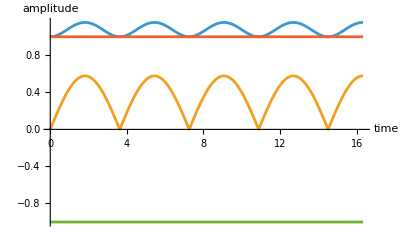

```mathematica
Plot[{Abs[x11],Abs[x22],-Abs[x11]^2+Abs[x22]^2,1},{t,0,5.2*Pi},AxesLabel->{time,amplitude}]
```